2

{{x2[t]→(5 ⅇ^(4+(-2-√5) t)-2 √5 ⅇ^(4+(-2-√5) t)-5 ⅇ^(8+2 √5+(-2-√5) t)+2 √5 ⅇ^(8+2 √5+(-2-√5) t)-5 ⅇ^(4+(2-√5) t)-2 √5 ⅇ^(4+(2-√5) t)+5 ⅇ^(2 √5+(2-√5) t)+2 √5 ⅇ^(2 √5+(2-√5) t))/(8 ⅇ^4)}}

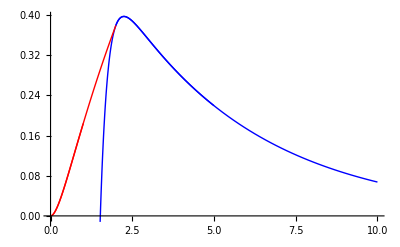

```mathematica
Remove["Global`*"];
soln1=DSolve[{x1''[t]+2 β x1'[t]+ω^2 x1[t]==a,x1[0]==0,x1'[0]==0},x1[t],t];
x1[t_]=x1[t]/.soln1;
(*Parameter Block*)
τ=2
a=β/τ;
ω=1;
β=Sqrt[5] ω;
(**************)
soln2=DSolve[{x2''[t]+2 β x2'[t]+ω^2 x2[t]==0,x2[τ]==x1[τ],x2'[τ]==x1'[τ]},x2[t],t]
x2[t_]=x2[t]/.soln2;
plot1[τ_]:=Plot[x1[t],{t,0,τ},PlotStyle->Red](*Driven*)
plot2[τ_]:=Plot[x2[t],{t,τ,5τ},PlotStyle->Blue] (*Not Driven*)
Show[{plot1[1],plot2[1],plot1[2],plot2[2]},PlotRange->All]
```